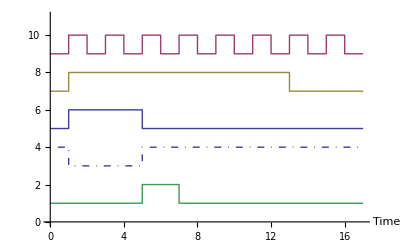

```mathematica
clock ={
{0,9},{1,9},{1,10},{2,10},
{2,9},{3,9},{3,10},{4,10},
{4,9},{5,9},{5,10},{6,10},
{6,9},{7,9},{7,10},{8,10},
{8,9},{9,9},{9,10},{10,10},
{10,9},{11,9},{11,10},{12,10},
{12,9},{13,9},{13,10},{14,10},
{14,9},{15,9},{15,10},{16,10},
{16,9},{17,9}};
periodicity ={
{0,7},{1,7},{1,8},{13,8},
{13,7},{17,7}};
delaypulse ={ 
{0,5},{1,5},{1,6},{5,6},
{5,5},{17,5}};
invdelaypulse ={ 
{0,4},{1,4},{1,3},{5,3},
{5,4},{17,4}};
delayedpulse ={ 
{0,1},{5,1},{5,2},{7,2},
{7,1},{17,1}};
sig=ListPlot[{delaypulse,clock,periodicity,delayedpulse},Joined->True,Axes->{True,False},PlotStyle->Thick,PlotRange->{All,{0,11}},AxesLabel->{"Time",None},LabelStyle->Bold];
invsig=ListPlot[{invdelaypulse},Joined->True,Axes->{True,False},PlotStyle->Directive[DotDashed,Thick],PlotRange->{All,{0,11}},AxesLabel->{"Time",None},LabelStyle->Bold];
Show[sig,invsig]
```

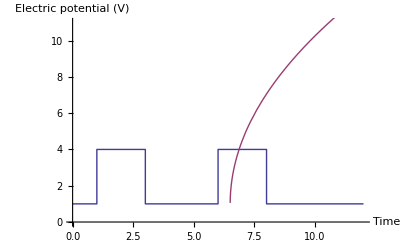

```mathematica
twopulses ={
{0,1},{1,1},{1,4},{3,4},{3,1},
{6,1},{6,4},{8,4},{8,1},{12,1}};
pls=ListPlot[twopulses,Joined->True,PlotStyle->Thick,PlotRange->{All,{0,11}},AxesLabel->{"Time","Electric potential (V)"},LabelStyle->Bold];
ion=Plot[1+7*Sqrt[(t-6.5)/2],{t,0,12},PlotStyle->Directive[ColorData[1,"ColorList"][[2]],Thick]];
Show[pls,ion]
```